```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
brzgamma=1.533*10^-3;
```

```mathematica
higgspreMuC={5.7,4.8,4.8,2.0,4.4,11,3.3,3,0.77,0.75,0.05}/100;(*{kw^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,1/7 kw^2 kt^2/ktotal+6/7 kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kz^2,kz^2brinv+1}*)
(*higgspreLHCratiosL={4.2,4.0,3.7,5.5,24.7,13.9,47.8,13.8,9.4,23.3,18.4,6.5,13.8,3.5}/100;*)(*{kg^2 kgamma^2/ktotal,kg^2 kz^2/ktotal,kg^2 kw^2/ktotal,kg^2 ktau^2/ktotal,kg^2 kb^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kz^2/ktotal,kw^2 kw^2/ktotal,kw^2 kb^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kb^2/ktotal,kg^2 kmu^2/ktotal}*)
higgspreLHCratiosL={4.2,4.0,3.7,5.5,24.7,13.8,12.8,13.4,7.3,4.4,54.0,13.9,47.8,13.8,9.4,23.3,78.6,18.4,6.5,9.4,24.6,9.7,11.6,14.9,2.2}/100;
(*{kg^2 kgamma^2/ktotal,kg^2 kz^2/ktotal,kg^2 kw^2/ktotal,kg^2 ktau^2/ktotal,kg^2 kb^2/ktotal,kg^2 kmu^2/ktotal,1/7 kw^2 kgamma^2/ktotal+6/7 kz^2 kgamma^2/ktotal,1/7 kw^2 kz^2/ktotal+6/7 kz^2 kz^2/ktotal,1/7 kw^2 kw^2/ktotal+6/7 kz^2 kw^2/ktotal,1/7 kw^2 ktau^2/ktotal+6/7 kz^2 ktau^2/ktotal,1/7 kw^2 kmu^2/ktotal+6/7 kz^2 kmu^2/ktotal,1/7 kw^2 kz^2/ktotal+6/7 kz^2 kz^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kz^2/ktotal,kw^2 kw^2/ktotal,kw^2 kb^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kb^2/ktotal,kt^2 kgamma^2/ktotal,kt^2 kz^2/ktotal,kt^2 kw^2/ktotal,kt^2 kb^2/ktotal,kt^2 ktau^2/ktotal,6/7kz^2brinv+1/7kw^2brinv+1}*)
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,99999(*Infinity*)(*(0.00401209+0.00402172)*100/2*),0.5}/100;
higgsobscepcinv=0.165/100;
halfcorrelation=(*06/14/2023*)SparseArray[{{10,10}->0}]//Normal;
inputcorrelations=(*06/14/2023*)IdentityMatrix[11]*100(*+halfcorrelationᵀ+halfcorrelation*);
(*halfcorrelationLHC=(*06/29/2023*)SparseArray[{{14,14}->0,{2,1}->48,{3,1}->54,{4,1}->46,{5,1}->-1,{7,1}->1,{8,1}->2,{10,1}->-3,{11,1}->6,{12,1}->2,{13,1}->14,{3,2}->52,{4,2}->37,{5,2}->-1,{6,2}->1,{7,2}->1,{8,2}->1,{9,2}->-1,{10,2}->1,{11,2}->6,{12,2}->2,{13,2}->13,{4,3}->42,{5,3}->-1,{6,3}-> 1,{11,3}->10,{12,3}-> 2,{13,3}-> 15,{5,4}-> -1,{6,4}-> 5,{7,4}-> 1,{8,4}-> 2,{10,4}-> 5,{11,4}-> 5,{12,4}-> 2,{13,4}-> 11,{9,5}-> -2,{12,5}-> -1,{8,6}-> 1,{10,6}-> -33,{10,8}-> 1,{11,8}-> -1,{12,9}-> 1,{12,10}-> -1,{12,11}-> -8}]//Normal;*)

halfcorrelationLHC=({{0, 48, 54, 46, -1, 14, -18, 2, -1, 2, 1, 0, 1, 2, 0, -3, 3, 6, 2, 8, 0, 2, 0, 1, 0}, {0, 0, 52, 37, -1, 13, 0, -11, -3, 0, -1, 1, 1, 1, -1, 1, -9, 6, 2, 1, 5, 1, 0, 1, 0}, {0, 0, 0, 42, -1, 15, -1, -2, -9, -1, -1, 1, 0, 0, 0, 0, -1, 10, 2, 1, 0, 2, 0, 1, 0}, {0, 0, 0, 0, -1, 11, 12, 5, 2, -16, 2, 5, 1, 2, 0, 5, 5, 5, 2, 3, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -2, 0, 0, 0, -1, -1, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 0, -53, 1, 0, 0, 0, 0, 1, 2, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 5, 6, 8, 1, 3, 0, 1, 0, 2, 2, 1, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 7, 7, 3, 2, 0, 1, 0, 2, 6, 0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 10, 1, 2, 0, 5, 0, 1, 0, 4, 0, 1, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2, 4, 1, 3, 0, 2, 1, 1, 0, 2, 1, 2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -33, 1, 0, 0, -5, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -68, 0, 0, 0, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -1, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -1, -6, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 1, -10, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -8, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 8, 18, 16, 11, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 5, 2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 14, -7, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 9, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});(*07/27/2023*)
inputcorrelationsLHC = (*07/27/2023*)IdentityMatrix[25]*100+halfcorrelationLHCᵀ+halfcorrelationLHC;
inverseinputcorrelations=Inverse[inputcorrelations/100];
inverseinputcorrelationsLHC=Inverse[inputcorrelationsLHC/100];
halfcorrelationcepc=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelationscepc=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationcepcᵀ+halfcorrelationcepc;
inverseinputcorrelationscepc=Inverse[inputcorrelationscepc/100];
```

```mathematica
higgsobsMuC10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kw^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,(*1/7 kw^2 kt^2/ktotal+6/7*)kw^2 kt^2/ktotal,kz^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquareMuC10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC[[i]])((higgsobsMuC10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgspreMuC]},{j,1,Length[higgspreMuC]}]

higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kgamma^2/ktotal,kg^2 kz^2/ktotal,kg^2 kw^2/ktotal,kg^2 ktau^2/ktotal,kg^2 kb^2/ktotal,kg^2 kmu^2/ktotal,1/7 kw^2 kgamma^2/ktotal+6/7 kz^2 kgamma^2/ktotal,1/7 kw^2 kz^2/ktotal+6/7 kz^2 kz^2/ktotal,1/7 kw^2 kw^2/ktotal+6/7 kz^2 kw^2/ktotal,1/7 kw^2 ktau^2/ktotal+6/7 kz^2 ktau^2/ktotal,1/7 kw^2 kmu^2/ktotal+6/7 kz^2 kmu^2/ktotal,1/7 kw^2 kz^2/ktotal+6/7 kz^2 kz^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kz^2/ktotal,kw^2 kw^2/ktotal,kw^2 kb^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kb^2/ktotal,kt^2 kgamma^2/ktotal,kt^2 kz^2/ktotal,kt^2 kw^2/ktotal,kt^2 kb^2/ktotal,kt^2 ktau^2/ktotal,6/7kz^2brinv+1/7kw^2brinv+1};
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};

chisquareMuC10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC[[i]])((higgsobsMuC10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgspreMuC]},{j,1,Length[higgspreMuC]}](*+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2*)+Sum[((higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHCratiosL[[i]])((higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHCratiosL[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHCratiosL]},{j,1,Length[higgspreLHCratiosL]}]
chisquareLHC10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHCratiosL[[i]])((higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHCratiosL[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHCratiosL]},{j,1,Length[higgspreLHCratiosL]}]
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
chisquareLHC10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHCratiosL[[i]])((higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHCratiosL[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHCratiosL]},{j,1,Length[higgspreLHCratiosL]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

Only MuC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
MuC10p//MatrixForm
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},MuC10p*100},3]ᵀ//MatrixForm
```

((0.0602451
-0.0511179)
(0.0179704
-0.0179216)
(0.0623978
-0.0535241)
(0.0608231
-0.0517628)
(0.0648285
-0.056255)
(0.00374299
-0.00375706)
(0.0648285
-0.0562549)
(0.0299025
-0.0304307)
(0.000500014
-0.000500014)
(0.124614
-0.100116))

(kb | {{6.02,-5.11}}
kt | {{1.8,-1.79}}
kg | {{6.24,-5.35}}
kw | {{6.08,-5.18}}
ktau | {{6.48,-5.63}}
kz | {{0.37,-0.38}}
kgamma | {{6.48,-5.63}}
kmu | {{2.99,-3.04}}
brinv | {{0.05,-0.05}}
ktotal | {{12.46,-10.01}})

### 10p-fit-MuC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
MuC10pL//MatrixForm
```

((0.0160371
-0.0157625)
(0.01569
-0.0156967)
(0.016454
-0.0164122)
(0.0142061
-0.0140808)
(0.0170778
-0.016966)
(0.00374299
-0.00375706)
(0.0163508
-0.0162803)
(0.0255992
-0.0260507)
(0.000499885
-0.000499885)
(0.0341283
-0.0329767))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},MuC10p*100,MuC10pL*100},3]ᵀ//MatrixForm
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@MuC10p,(#[[1,1]]-#[[1,2]])/2*100&/@MuC10pL},2]ᵀ//MatrixForm
```

(kb | {{6.02,-5.11}} | {{1.6,-1.58}}
kt | {{1.8,-1.79}} | {{1.57,-1.57}}
kg | {{6.24,-5.35}} | {{1.65,-1.64}}
kw | {{6.08,-5.18}} | {{1.42,-1.41}}
ktau | {{6.48,-5.63}} | {{1.71,-1.7}}
kz | {{0.37,-0.38}} | {{0.37,-0.38}}
kgamma | {{6.48,-5.63}} | {{1.64,-1.63}}
kmu | {{2.99,-3.04}} | {{2.56,-2.61}}
brinv | {{0.05,-0.05}} | {{0.05,-0.05}}
ktotal | {{12.46,-10.01}} | {{3.41,-3.3}})

(kb | 5.6 | 1.6
kt | 1.8 | 1.6
kg | 5.8 | 1.6
kw | 5.6 | 1.4
ktau | 6.1 | 1.7
kz | 0.4 | 0.4
kgamma | 6.1 | 1.6
kmu | 3. | 2.6
brinv | 0.05 | 0.05
ktotal | 11.2 | 3.4)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@MuC10p
(#[[1,1]]-#[[1,2]])/2&/@MuC10pL
```

{0.0556815,0.017946,0.0579609,0.0562929,0.0605418,0.00375003,0.0605417,0.0301666,0.000500014,0.112365}

{0.0158998,0.0156934,0.0164331,0.0141435,0.0170219,0.00375003,0.0163156,0.0258249,0.000499885,0.0335525}

skip below

```mathematica
concentrationmatrix10pL=Table[D[chisquareMuC10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@MuC10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@MuC10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00004 | 0.587306 | 0.888449 | 0.89504 | 0.931422 | 0.242999 | 0.170569 | 0.079863 | 0. | 0.972108
0.587306 | 0.999853 | 0.480479 | 0.534928 | 0.561192 | 0.131537 | 0.100895 | 0.0475803 | 0. | 0.581922
0.888449 | 0.480479 | 1.00002 | 0.817183 | 0.844922 | 0.207507 | 0.153268 | 0.072064 | 0. | 0.879634
0.89504 | 0.534928 | 0.817183 | 1.00007 | 0.831244 | 0.231195 | 0.157685 | 0.0736481 | 0. | 0.894973
0.931422 | 0.561192 | 0.844922 | 0.831244 | 1.00002 | 0.213239 | 0.159251 | 0.0749429 | 0. | 0.915309
0.242999 | 0.131537 | 0.207507 | 0.231195 | 0.213239 | 0.999994 | 0.153555 | 0.050151 | 0. | 0.43334
0.170569 | 0.100895 | 0.153268 | 0.157685 | 0.159251 | 0.153555 | 0.999969 | 0.0174489 | 0. | 0.191394
0.079863 | 0.0475803 | 0.072064 | 0.0736481 | 0.0749429 | 0.050151 | 0.0174489 | 0.999778 | 0. | 0.0851411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999979 | 0.
0.972108 | 0.581922 | 0.879634 | 0.894973 | 0.915309 | 0.43334 | 0.191394 | 0.0851411 | 0. | 0.999929)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00002,0.999926,1.00001,1.00004,1.00001,0.999997,0.999985,0.999889,0.99999,0.999964}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

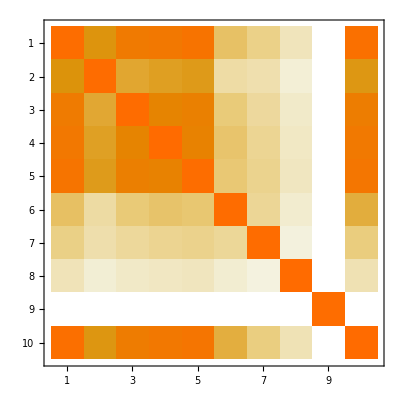

```mathematica
MatrixPlot[correlationmatrix10pL]
```

skip above

```mathematica
MuC10p=Table[MuC10p[[i,1,1]]/2-MuC10p[[i,1,2]]/2,{i,1,Length[MuC10p]}]
MuC10pL=Table[MuC10pL[[i,1,1]]/2-MuC10pL[[i,1,2]]/2,{i,1,Length[MuC10pL]}]
```

{0.0556815,0.017946,0.0579609,0.0562929,0.0605418,0.00375003,0.0605417,0.0301666,0.000500014,0.112365}

{0.0158998,0.0156934,0.0164331,0.0141435,0.0170219,0.00375003,0.0163156,0.0258249,0.000499885,0.0335525}

```mathematica
MuC10data={Table[If[i==Length[MuC10p]-1,MuC10p[[i]]*2,If[i==Length[MuC10p],MuC10p[[i]],MuC10p[[i]]]],{i,1,Length[MuC10p]}],Table[If[i==Length[MuC10pL]-1,MuC10pL[[i]]*2,If[i==Length[MuC10pL],MuC10pL[[i]],MuC10pL[[i]]]],{i,1,Length[MuC10pL]}]}
```

{{0.0556815,0.017946,0.0579609,0.0562929,0.0605418,0.00375003,0.0605417,0.0301666,0.00100003,0.112365},{0.0158998,0.0156934,0.0164331,0.0141435,0.0170219,0.00375003,0.0163156,0.0258249,0.00099977,0.0335525}}

below is for plot only MuC

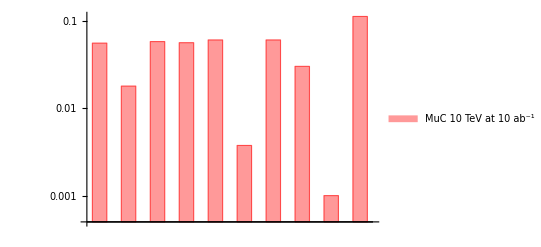

```mathematica
data={MuC10data[[1]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10=BarChart[%ᵀ,ScalingFunctions->"Log",FrameLabel->{{"Relative Error δX/X",None},{None,"Precision of Higgs coupling measurement"}},GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{Directive[EdgeForm[Dashed],Opacity[0.4],Red]},BaseStyle->12,PlotRange->{Automatic,{5*10^-4,1}},BarSpacing->{0,1},FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["MuC 10 TeV at 10 \!\(\*SuperscriptBox[\(ab\), \(-1\)]\)",20]},Scaled[{{0.02,0.8},{0,0}}]]]
```

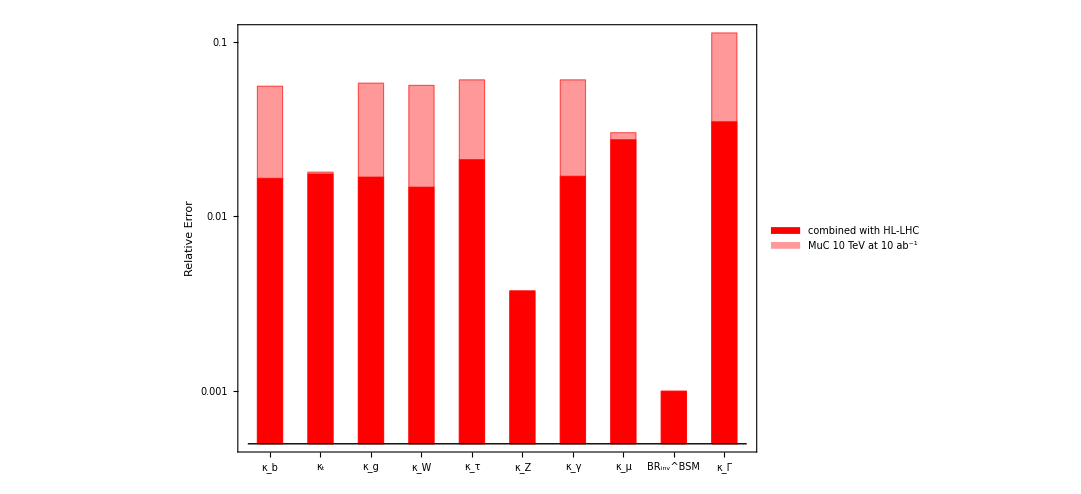

```mathematica
data={MuC10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"\!\(\*SubscriptBox[\(κ\), \(b\)]\)","\!\(\*SubscriptBox[\(κ\), \(t\)]\)","\!\(\*SubscriptBox[\(κ\), \(g\)]\)","\!\(\*SubscriptBox[\(κ\), \(W\)]\)","\!\(\*SubscriptBox[\(κ\), \(τ\)]\)","\!\(\*SubscriptBox[\(κ\), \(Z\)]\)","\!\(\*SubscriptBox[\(κ\), \(γ\)]\)","\!\(\*SubscriptBox[\(κ\), \(μ\)]\)",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(BSM\)]\)",25],"\!\(\*SubscriptBox[\(κ\), \(Γ\)]\)"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-3,1}],1]},ChartStyle->{{},{Red,Red}},BaseStyle->28,PlotRange->{{0.5,20.5},{5*10^-4,1}},BarSpacing->{0,1},FrameTicks->{{{{0.001,"\!\(\*SuperscriptBox[\(10\), \(-3\)]\)"},{0.01,"\!\(\*SuperscriptBox[\(10\), \(-2\)]\)"},{0.1,"\!\(\*SuperscriptBox[\(10\), \(-1\)]\)"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ChartLegends->Placed[{Style["combined with HL-LHC",20]},Scaled[{{0.02,0.7},{0,0}}]],ImageSize->800];
Show[p100,p10]
```

Only LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
LHC10p//MatrixForm
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},LHC10p*100},3]ᵀ//MatrixForm
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {brinv,kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {0.618381,1.7426,1.81554,1.02898,0.705467,1.51602,1.23152,1.60226,1.40791,0.936109}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.+«12»+2.24135 (-1+(kg^2 kgamma^2)/ktotal) (-1+(kt^2 kw^2)/ktotal)-1.0305 (-1+(kg^2 kgamma^2)/ktotal) (-1+kw^4/ktotal)+«15» encountered.

Infinity::indet: Indeterminate expression 0.-248.332 (-1+(kg^2 kgamma^2)/ktotal) (-1+(kg^2 kz^2)/ktotal)-11.8183 (-1+(kg^2 kmu^2)/ktotal) (-1+(kg^2 kz^2)/ktotal)+8.01837 (-1+(kgamma^2 kt^2)/ktotal) (-1+(kg^2 kz^2)/ktotal)-89.4797 (-1+((«2»)^2 «1»)/ktotal) (-1+(kg^2 kz^2)/ktotal)-«1»-«1»+8.74652 (-1+(kgamma^2 kw^2)/ktotal) (-1+(kg^2 kz^2)/ktotal)-0.752961 (-1+(kt^2 kw^2)/ktotal) (-1+(kg^2 kz^2)/ktotal)+4.26736 (-1+kw^4/ktotal) (-1+(kg^2 kz^2)/ktotal)+«15» encountered.

Infinity::indet: Indeterminate expression 0.-355.177 (-1+(kg^2 kgamma^2)/ktotal) (-1+(kg^2 kw^2)/ktotal)-19.021 (-1+(kg^2 kmu^2)/ktotal) (-1+(kg^2 kw^2)/ktotal)+12.9654 (-1+(kgamma^2 kt^2)/ktotal) (-1+(kg^2 kw^2)/ktotal)-129.871 (-1+(«1» «1»)/ktotal) (-1+(kg^2 kw^2)/ktotal)-«1»+«19» «1»+1.91884 (-1+(kg^2 kw^2)/ktotal) (-1+(kgamma^2 kw^2)/ktotal)-6.68861 (-1+(kg^2 kw^2)/ktotal) (-1+(kt^2 kw^2)/ktotal)-1.37883 (-1+(kg^2 kw^2)/ktotal) (-1+kw^4/ktotal)+«15» encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {brinv,kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {0.618381,1.7426,1.81554,1.02898,0.705467,1.51602,1.23152,1.60226,1.40791,0.936109}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {brinv,kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {0.618381,1.7426,1.81554,1.02898,0.705467,1.51602,1.23152,1.60226,1.40791,0.936109}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {brinv,kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {0.618381,1.7426,1.81554,1.02898,0.705467,1.51602,1.23152,1.60226,1.40791,0.936109}.

Power::infy: Infinite expression 1/0. encountered.

NMinimize::nnum: The function value Indeterminate is not a number at {brinv,kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {0.618381,1.7426,1.81554,1.02898,0.705467,1.51602,1.23152,1.60226,1.40791,0.936109}.

Power::infy: Infinite expression 1/0. encountered.

$Aborted

LHC10p

Transpose::nmtx: {{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},100. LHC10p} 的前两层无法转置.

Transpose[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},100. LHC10p}]

LHC+CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
LHC10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareLHC10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareLHC10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
LHC10pL//MatrixForm
(*SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},LHC10p*100,LHC10pL*100},3]ᵀ//MatrixForm
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@MuC10p,(#[[1,1]]-#[[1,2]])/2*100&/@MuC10pL},2]ᵀ//MatrixForm*)
```

((0.00926573
-0.00924513)
(0.0177786
-0.0178626)
(0.011709
-0.0116804)
(0.00958006
-0.00958466)
(0.0105013
-0.0104642)
(0.00249687
-0.00250313)
(0.0145026
-0.0146424)
(0.0417878
-0.0434869)
(0.0016454
-0.0016454)
(0.0209632
-0.020649))

Only CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.013196
-0.0131098)
(0.0233468
-0.0232453)
(0.0165965
-0.0164075)
(0.0138349
-0.0137875)
(0.0149305
-0.014782)
(0.00249668
-0.00250313)
(0.0432081
-0.0444282)
(0.0780118
-0.0838382)
(0.00165002
-0.00165002)
(0.028958
-0.028282))

```mathematica
(*(#[[1,1]]-#[[1,2]])/2&/@LHC10p*)
(#[[1,1]]-#[[1,2]])/2&/@LHC10pL
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.00925543,0.0178206,0.0116947,0.00958236,0.0104827,0.0025,0.0145725,0.0426374,0.0016454,0.0208061}

{0.0131529,0.023296,0.016502,0.0138112,0.0148562,0.00249991,0.0438181,0.080925,0.00165002,0.02862}

```mathematica
LHC10p=Table[LHC10p[[i,1,1]]/2-LHC10p[[i,1,2]]/2,{i,1,Length[LHC10p]}]
LHC10pL=Table[LHC10pL[[i,1,1]]/2-LHC10pL[[i,1,2]]/2,{i,1,Length[LHC10pL]}]
cepc10p=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
```

{}

{0.00925543,0.0178206,0.0116947,0.00958236,0.0104827,0.0025,0.0145725,0.0426374,0.0016454,0.0208061}

{0.0131529,0.023296,0.016502,0.0138112,0.0148562,0.00249991,0.0438181,0.080925,0.00165002,0.02862}

```mathematica
LHC10data={Table[If[i==Length[LHC10p]-1,LHC10p[[i]]*2,If[i==Length[LHC10p],LHC10p[[i]],LHC10p[[i]]]],{i,1,Length[LHC10p]}],Table[If[i==Length[LHC10pL]-1,LHC10pL[[i]]*2,If[i==Length[LHC10pL],LHC10pL[[i]],LHC10pL[[i]]]],{i,1,Length[LHC10pL]}]}
cepc10data={Table[If[i==Length[cepc10p]-1,cepc10p[[i]]*2,If[i==Length[cepc10p],cepc10p[[i]],cepc10p[[i]]]],{i,1,Length[cepc10p]}]}
```

{{},{0.00925543,0.0178206,0.0116947,0.00958236,0.0104827,0.0025,0.0145725,0.0426374,0.0032908,0.0208061}}

{{0.0131529,0.023296,0.016502,0.0138112,0.0148562,0.00249991,0.0438181,0.080925,0.00330004,0.02862}}

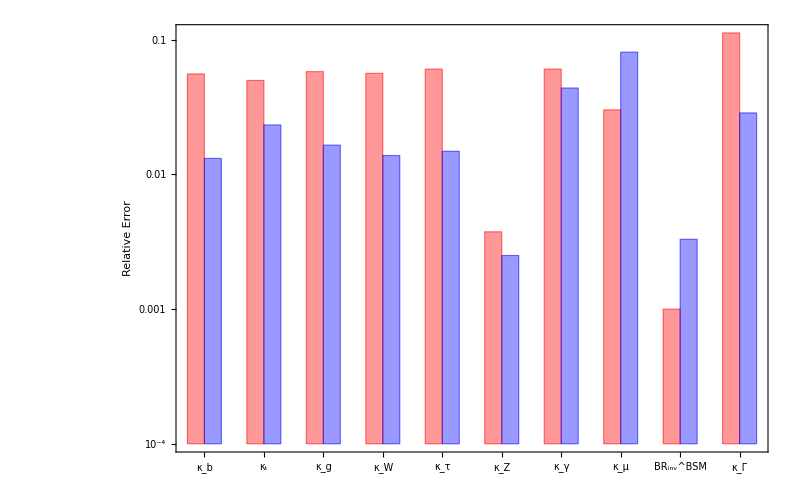

```mathematica
data={MuC10data[[1]],cepc10data[[1]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p10LHC=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(BSM\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (9-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{Red,Blue,Magenta}},BaseStyle->28,PlotRange->{{1,41},{1*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

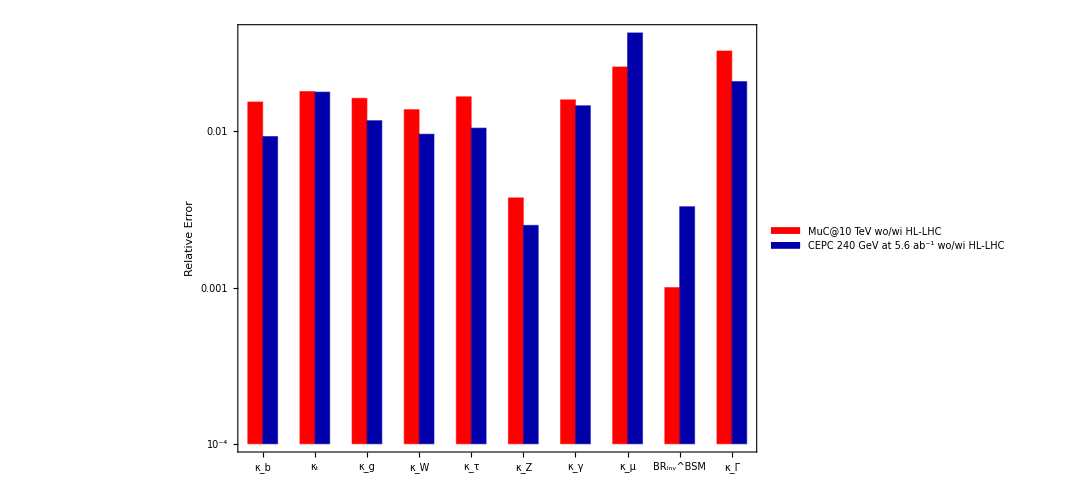

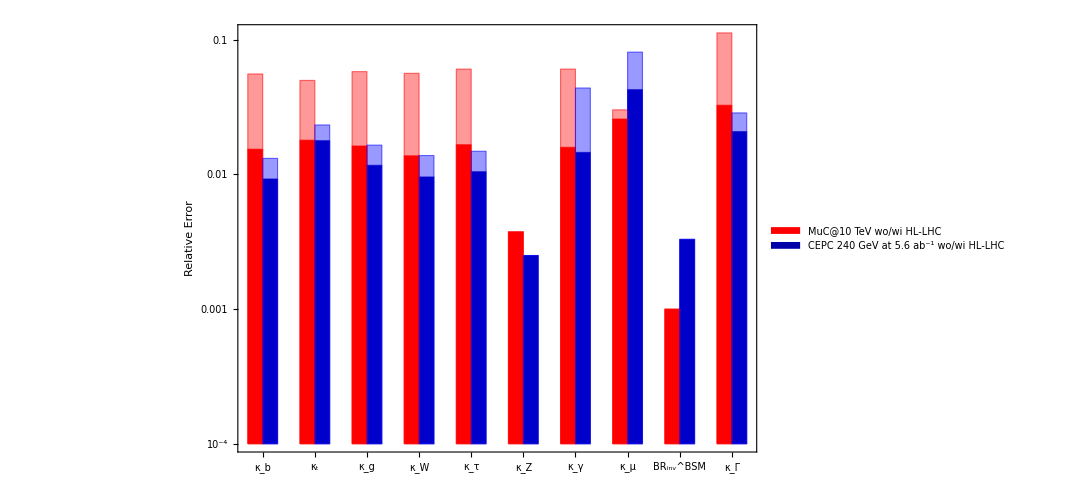

```mathematica
data={MuC10data[[2]],LHC10data[[2]]};
plot=Table[Table[data[[j,i]],{i,1,Length[data[[1]]],1}],{j,1,Length[data],1}];
p100LHC=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(BSM\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,9},{j,-4,1}],1]},ChartStyle->{Red,Darker[Blue],Magenta},BaseStyle->28,PlotRange->{{1,41},{1*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800,ChartLegends->Placed[{Style["MuC@10 TeV wo/wi HL-LHC",20],Style["CEPC 240 GeV at 5.6 ab^-1 wo/wi HL-LHC",20]},Scaled[{{0.2,0.75},{0,0}}]]]
Show[p100LHC,p10LHC]
```